\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## BI-BEZ – Security – Lab 1 Tomáš Zahradnický, Jiří Buček Department of computer systems, FIT CTU in Prague

Intro to Mathematica (recap)

Substitution cipher

Affine cipher

Transposition cipher

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Gentle introduction to the Mathematica software

In the labs, we will use Mathematica for demonstration of ciphers and their cryptanalysis. Therefore it is important to learn using Mathematica at least in a basic way.

Mathematica is divided into the Front End (this) and the Kernel (not visible). The Front End sends commands denotec In[number] to the kernel and receives the output of the kernel, denoted Out[number]. To launch the command In[number] (send to the kernel for evaluation), press the key combination SHIFT+ENTER, or  ENTER on the numpad.

Before we begin, Mathematica is case sensitive and cares about parentheses strictly so take care. Round parentheses signify the evaluation priority, whereas square brackets denote function arguments, and curly brackets denote vectors, matrices and lists.

Now try evaluating the following expressions:

```mathematica
1-1
```

0

```mathematica
Mod[283,17]
```

11

```mathematica
Sin[Pi/2]
```

1

```mathematica
Sum[1/i^2,{i,1,∞}]
```

π^2/6

```mathematica
Mod[102*BEZInverse[102,113],113]
```

1

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Worksheet initialization

In order to use the programs in this presentation, we must perform initialization. Click anywhere into the following block and let it evaluate. The block defines functions that will be used for ciphering, deciphering, and analysis. You do not need to study them.

```mathematica
<<"BarCharts`";
NCharacters=26;
SYMBOLS=Table[FromCharacterCode[65+i],{i,0,57}];
ENGLISH={0.0805726131341181993`1.9999999999999998,0.0125943599170806117`1.9999999999999998,0.0362576759103531896`1.9999999999999976,0.0380959831032189932`1.9999999999999998,0.1146790784996284273`1.9999999999999998,0.0240935581022411703`1.9999999999999998,0.0157233934368521923`1.9999999999999998,0.031212109359721516`1.9999999999999998,0.0741972073375836039`1.9999999999999998,0.001290726326905777`1.9999999999999998,0.0015254038408886455`1.9999999999999998,0.0429459850588649431`1.9999999999999998,0.0222943638283725115`1.9999999999999998,0.0746274494465521962`1.9999999999999998,0.0873782610396213869`1.9999999999999998,0.0389955802401533226`1.9999999999999998,0.0010169358939257637`1.9999999999999976,0.0751750303125122228`1.9999999999999998,0.0571830875738256346`1.9999999999999998,0.0912504400203387179`1.9999999999999998,0.0322290452536472797`1.9999999999999998,0.0081746000704032542`1.9999999999999998,0.0116165369421519928`1.9999999999999976,0.0017991942738686588`1.9999999999999998,0.0243282356162240388`1.9999999999999998,0.0007431454609457504`1.9999999999999998};
VelikostAbecedy[n_Integer]:=Module[{},NCharacters=n;Take[SYMBOLS,n]]
BEZRotChar[x_,amount_]:=FromCharacterCode[Mod[(ToCharacterCode[x]-ToCharacterCode["A"])+amount,NCharacters]+ToCharacterCode["A"]]
AXPBChar[x_,a_,b_]:=FromCharacterCode[Mod[(ToCharacterCode[x]-ToCharacterCode["A"]) a+b,NCharacters]+ToCharacterCode["A"]]
AXPB::notcoprime="Multiplicative coefficient not coprime to modulus. Information will be lost.";
AXPB[x_String,a_,b_]:=Block[{},If[GCD[a,NCharacters]≠1,Message[AXPB::notcoprime]];StringJoin[(AXPBChar[#1,a,b]&)/@Characters[BEZPrepText[x]]]];
AXPBDecrypt[x_String,a_,b_]:=StringJoin[(AXPBCharDecrypt[#1,a,b]&)/@Characters[x]]
BEZZnakPlusB[x_String,b_Integer]:=(BEZRotChar[#1,b]&)/@Characters[x]
AXPBCharDecrypt[x_,a_,b_]:=FromCharacterCode[Mod[((ToCharacterCode[x]-ToCharacterCode["A"])-b) BEZInverse[a,NCharacters],NCharacters]+ToCharacterCode["A"]]
BEZInverse[x_Integer,mod_]:=Inverse[{{x}},Modulus->mod]⟦1⟧⟦1⟧
Caesar[x_String,posun_]:=StringJoin[BEZZnakPlusB[x,posun]]
BEZPrepText[x_String]:=FromCharacterCode[Select[(#1⟦1⟧&)/@ToCharacterCode[Characters[ToUpperCase[x]]],0≤#1-ToCharacterCode["A"]⟦1⟧≤NCharacters&]]
BEZAbsCetnosti[x_String]:=Table[Length[Select[Characters[BEZPrepText[x]],#1===SYMBOLS⟦i⟧&]],{i,1,NCharacters}]
BEZRelFreq[x_String]:=N[BEZAbsCetnosti[x]/StringLength[BEZPrepText[x]],2]

RelFreq[x_String]:=TableForm[Module[{X},X=BEZRelFreq[x];Append[Table[Table[{SYMBOLS⟦7 i+j⟧,X⟦7 i+j⟧},{j,1,7}],{i,0,-1+Floor[NCharacters/7]}],Table[{SYMBOLS⟦7 Floor[NCharacters/7]+i⟧,X⟦7 Floor[NCharacters/7]+i⟧},{i,1,Mod[NCharacters,7]}]]]]
BEZGraphRelFreq[x_String,y_String]:=Module[{RC1,RC2},RC1=BEZRelFreq[x];RC2=BEZRelFreq[y];BarChart[{RC1,RC2},BarLabels->SYMBOLS,BarEdges->False,BarStyle->{Directive[RGBColor[.1,.2,.7],Opacity[0.7]],Directive[RGBColor[0,.7,0],Opacity[0.7]]},BarSpacing->0.1,Background->GrayLevel[.9]]]
BEZGraphRelFreqWEnglish[x_String]:=Module[{RC1,RC2},RC1=BEZRelFreq[x];RC2=ENGLISH;BarChart[{RC1,RC2},BarLabels->SYMBOLS,BarEdges->False,BarStyle->{Directive[RGBColor[.1,.2,.7],Opacity[0.7]],Directive[RGBColor[0,.7,0],Opacity[0.7]]},BarSpacing->0.1,Background->GrayLevel[.9]]]
RelFreqZBEZRelFreq[x_]:=TableForm[{Table[{FromCharacterCode[64+i],x⟦i⟧},{i,7}],Table[{FromCharacterCode[64+i],x⟦i⟧},{i,8,14}],Table[{FromCharacterCode[64+i],x⟦i⟧},{i,15,21}],Table[{FromCharacterCode[64+i],x⟦i⟧},{i,22,26}]}]
Pozice[x_String]:=StringPosition[StringJoin[SYMBOLS],x]⟦1⟧⟦1⟧-1
BEZPadString[x_String,n_Integer]:=If[StringLength[x]<n,BEZPadString[StringJoin[x,"X"],n], If[StringLength[x]==n, x, Abort[]]]
BEZNumToPad[x_String,cols_Integer]:=Floor[(StringLength[x]+cols-1)/cols]*cols
BEZGenerMatrix[x_String,cols_Integer]:=Partition[Characters[BEZPadString[BEZPrepText[x],BEZNumToPad[BEZPrepText[x],cols]]],cols]
BEZTranspose[x_String,cols_Integer]:=StringJoin[Flatten[Transpose[BEZGenerMatrix[BEZPrepText[x],cols]]]]

Print["Initialization done"]
```

General::obspkg: BarCharts` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Initialization done

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Simple Ciphers (Caesar)

Caesar cipher is known as a simple substitution stream (character) cipher that performs the transformation y = |x+3|_26. Let us have this plaintext (let it evaluate)

```mathematica
PT:="ANOPENTEXTTHATWILLGETTRANSFORMEDWITHCAESARCIPHER"
```

Ciphertext will be:

```mathematica
CT=Caesar[PT,3]
```

DQRSHQWHAWWKDWZLOOJHWWUDQVIRUPHGZLWKFDHVDUFLSKHU

Ciphertext can be easily decrypted performing the reverse transformation (subtraction):

```mathematica
Caesar[CT,-3]
```

ANOPENTEXTTHATWILLGETTRANSFORMEDWITHCAESARCIPHER

Cryptanalysis of this cipher follows on the next slide.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Cryptanalysis of the Caesar Cipher

Relative frequency of individual characters of the alphabet in the ciphertext from the previous slide is:

```mathematica
RelFreq[CT]
```

RelFreq[CT]

Relative frequency in the plaintext:

```mathematica
RelFreq[PT]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Cryptanalysis of the Caesar Cipher (2)

Comparing the relative frequencies (blue for ciphertext, green for plaintext), we see the shift in the frequencies caused by the cipher:

```mathematica
BEZGraphRelFreq[CT,PT]
```

It is evident form the graph that with known plaintext, it is trivial to guess the correct transformation. It suffices to shift the frequencies so that the graphs overlap. If we would not have the plaintext, we would have to make do with frequency distribution characteristic for the assumed language used. We assume that the plaintext was written in English, whose relative frequencies were analyzed in advance and are available in the variable called ENGLISH.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Cryptanalysis of the Caesar Cipher (3)

Relative frequencies for English are (gathered from ca. 20KB file):

```mathematica
RelFreqZBEZRelFreq[ENGLISH]
```

Now let us do the same graphical comparison as before but with only knowing the language (not plaintext):

```mathematica
BEZGraphRelFreqWEnglish[CT]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Task 1: Find the planitext for this ciphertext

The unknown ciphertext CT is:

```mathematica
CT="BAGURNGGRZCGAHZOREGUERRABGONQPBATENGHYNGVBAF"
```

BAGURNGGRZCGAHZOREGUERRABGONQPBATENGHYNGVBAF

```mathematica
Caesar[CT, 13]
```

ONTHEATTEMPTNUMBERTHREENOTBADCONGRATULATIONS

Analyze relative frequency of characters in the ciphertext and find the correct plaintext. The cipher used is a variant of the Caesar cipher.

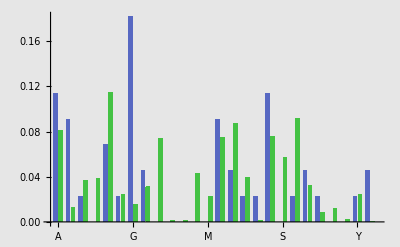

```mathematica
BEZGraphRelFreqWEnglish[CT]
```

Hint: Compare relative frequency. The CT variable is global, you can use the expressions on previous slides in any way you wish.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Ciphers |ap+b|_m

Caesar cipher is a special case of the affine transformation |ap+b|_m and is defined as |p+b|_m. This cipher is also a substitution, however this substitution does not only shift the graph of relative frequencies, but it causes better “mixing” (see the graph below). Let us give an example:

```mathematica
PT="THISISYETANOTHERCIPHERTEXTTHATWEWILLENCIPHER"
```

```mathematica
CT=AXPB[PT,5,19]
```

```mathematica
BEZGraphRelFreq[CT,PT]
```

We can now decrypt this text by reversing the cipher expression, i.e. if we have y=|ap+b|_m, we get p=|a^-1(y-b)|_m.

```mathematica
AXPBDecrypt[CT,5,19]
```

We can however also use the original formula (the form with multiplication and addition) p=|□ c + □|_m. How can we do that? Write a generic formula (using substitution). With specific values:

```mathematica
AXPB[CT,21,17]
```

How many unique keys are there for the alphabet of m letters?

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Task 2: Cryptanalysis of the cipher |ap+b|_m

1. Select two random constants a and b, and encrypt an English text of at least 100 characters. Such text can be found for example in any software documentation. Once you have a cryptogram, send it to your neighbo (e.g. by email), but do not tell him/her your constants!

```mathematica
PT="WHEREASRECOGNITIONOFTHEINHERENTDIGNITYANDOFTHEEQUALAND\\
INALIENABLERIGHTSOFALLMEMBERSOFTHEHUMANFAMILYISTHE\\
FOUNDATIONOFFREEDOMJUSTICEANDPEACEINTHEWORLD
WHEREASDISREGARDANDCONTEMPTFORHUMANRIGHTSHAVERESULTEDIN\\
BARBAROUSACTSWHICHHAVEOUTRAGEDTHECONSCIENCEOFMANKINDANDTHE\\
ADVENTOFAWORLDINWHICHHUMANBEINGSSHALLENJOYFREEDOMOFSPEECH\\
ANDBELIEFANDFREEDOMFROMFEARANDWANTHASBEENPROCLAIMEDASTHE\\
HIGHESTASPIRATIONOFTHECOMMONPEOPLE
WHEREASITISESSENTIALIFMANISNOTTOBECOMPELLEDTOHAVE\\
RECOURSEASALASTRESORTTOREBELLIONAGAINSTTYRANNYAND\\
OPPRESSIONTHATHUMANRIGHTSSHOULDBEPROTECTEDBYTHERULEOFLAW
WHEREASITISESSENTIALTOPROMOTETHEDEVELOPMENTOFFRIENDLY\\
RELATIONSBETWEENNATIONS
WHEREASTHEPEOPLESOFTHEUNITEDNATIONSHAVEINTHECHARTER\\
REAFFIRMEDTHEIRFAITHINFUNDAMENTALHUMANRIGHTSINTHEDIGNITY\\
ANDWORTHOFTHEHUMANPERSONANDINTHEEQUALRIGHTSOFMENAND\\
WOMENANDHAVEDETERMINEDTOPROMOTESOCIALPROGRESSANDBETTER\\
STANDARDSOFLIFEINLARGERFREEDOM
WHEREASMEMBERSTATESHAVEPLEDGEDTHEMSELVESTOACHIEVEIN\\
COOPERATIONWITHTHEUNITEDNATIONSTHEPROMOTIONOFUNIVERSAL\\
RESPECTFORANDOBSERVANCEOFHUMANRIGHTSANDFUNDAMENTALFREEDOMS
WHEREASACOMMONUNDERSTANDINGOFTHESERIGHTSANDFREEDOMSISOFTHE\\
GREATESTIMPORTANCEFORTHEFULLREALIZATIONOFTHISPLEDGE";
a=9;
b=22;
```

```mathematica
CT=AXPB[PT,a,b]
```

MHGTGWCTGOSYJQLQSJSPLHGQJHGTGJLXQYJQLEWJXSPLHGGKUWRWJXQJWRQGJWFRGTQYHLCSPWRRAGAFGTCSPLHGHUAWJPWAQREQCLHGPSUJXWLQSJSPPTGGXSAZUCLQOGWJXBGWOGQJLHGMSTRXMHGTGWCXQCTGYWTXWJXOSJLGABLPSTHUAWJTQYHLCHWDGTGCURLGXQJFWTFWTSUCWOLCMHQOHHWDGSULTWYGXLHGOSJCOQGJOGSPAWJIQJXWJXLHGWXDGJLSPWMSTRXQJMHQOHHUAWJFGQJYCCHWRRGJZSEPTGGXSASPCBGGOHWJXFGRQGPWJXPTGGXSAPTSAPGWTWJXMWJLHWCFGGJBTSORWQAGXWCLHGHQYHGCLWCBQTWLQSJSPLHGOSAASJBGSBRGMHGTGWCQLQCGCCGJLQWRQPAWJQCJSLLSFGOSABGRRGXLSHWDGTGOSUTCGWCWRWCLTGCSTLLSTGFGRRQSJWYWQJCLLETWJJEWJXSBBTGCCQSJLHWLHUAWJTQYHLCCHSURXFGBTSLGOLGXFELHGTURGSPRWMMHGTGWCQLQCGCCGJLQWRLSBTSASLGLHGXGDGRSBAGJLSPPTQGJXRETGRWLQSJCFGLMGGJJWLQSJCMHGTGWCLHGBGSBRGCSPLHGUJQLGXJWLQSJCHWDGQJLHGOHWTLGTTGWPPQTAGXLHGQTPWQLHQJPUJXWAGJLWRHUAWJTQYHLCQJLHGXQYJQLEWJXMSTLHSPLHGHUAWJBGTCSJWJXQJLHGGKUWRTQYHLCSPAGJWJXMSAGJWJXHWDGXGLGTAQJGXLSBTSASLGCSOQWRBTSYTGCCWJXFGLLGTCLWJXWTXCSPRQPGQJRWTYGTPTGGXSAMHGTGWCAGAFGTCLWLGCHWDGBRGXYGXLHGACGRDGCLSWOHQGDGQJOSSBGTWLQSJMQLHLHGUJQLGXJWLQSJCLHGBTSASLQSJSPUJQDGTCWRTGCBGOLPSTWJXSFCGTDWJOGSPHUAWJTQYHLCWJXPUJXWAGJLWRPTGGXSACMHGTGWCWOSAASJUJXGTCLWJXQJYSPLHGCGTQYHLCWJXPTGGXSACQCSPLHGYTGWLGCLQABSTLWJOGPSTLHGPURRTGWRQNWLQSJSPLHQCBRGXYG

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Task 2: Cryptanalysis of the cipher |ap+b|_m (2)

2. After you get the ciphertext from your neighbor, assign its value to the CT variable:

```mathematica
CT="JPTJMLCTPCAPVAZKLVEAJVTJCQHPCAZVZZLMJVAZYKJCQHPCAZFPKBPEPKKLMJIAZTLWZVFJKKAZIPKKJVAZPKJWZLMQZPQAPVAZEALNRAEVFJEAJCAJVAZPQFZKKSNVEUPVVAJTEAZMZFAXVALNKQFZZWZCHPMZAZFPVENMCZQELVEZZKJCEAZRMZPETPRCZEJHIJZKQFAZMZAZEMPWZKZQEJTZILMEAZINENMZLITPCBJCQCLYLQXFPCEVAJTAZSNVEVEPMZVPEEAZFLMKQUKPCCJCRAJVWZCRZPCHZEAPEAZFJKKVLLCNCINMKCLFEAZEJTZJVAZMZILMJMLCTPCELVUMZPQIZPMWZCRZPCHZIMLTEAZRMPWZBJKKVEAZUZLUKZAZLCHZVPWZQCLYLQXFPCEVAJTEAZXSNVEENMCEAZJMAZPQVCLYLQXAZKUVAJTCLFAZAPVAJVMZWZCRZAZPWXYLLEVLIKZPQIJKKVAJVWJHEJTVINKKLIQMZPQMNCCJCRPVIPVEPVEAZXHPCJMLCTPCKJWZVPRPJC";
```

Analyze the frequencies:

```mathematica
RelFreq[CT]
```

A
0.087 | B
0.0055 | C
0.075 | D
0 | E
0.069 | F
0.025 | G
0
H
0.016 | I
0.027 | J
0.071 | K
0.056 | L
0.06 | M
0.051 | N
0.024
O
0 | P
0.082 | Q
0.036 | R
0.018 | S
0.0055 | T
0.029 | U
0.011
V
0.073 | W
0.022 | X
0.013 | Y
0.0091 | Z
0.13 |  |

And compare them with the English language:

```mathematica
RelFreqZBEZRelFreq[ENGLISH]
```

A
0.081 | B
0.013 | C
0.036 | D
0.038 | E
0.11 | F
0.024 | G
0.016
H
0.031 | I
0.074 | J
0.0013 | K
0.0015 | L
0.043 | M
0.022 | N
0.075
O
0.087 | P
0.039 | Q
0.001 | R
0.075 | S
0.057 | T
0.091 | U
0.032
V
0.0082 | W
0.012 | X
0.0018 | Y
0.024 | Z
0.00074 |  |

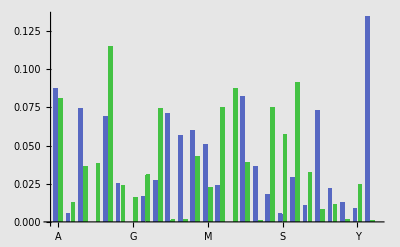

```mathematica
BEZGraphRelFreqWEnglish[CT]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Task 2: Cryptanalysis of the cipher |ap+b|_m (3)

From the frequency analysis, we have determined the most frequent characters in English to be E and T. We can use this to derive the decryption key. We take two most frequent characters in the ciphertext and try mapping them to E and T. Solving a system of 2 linear equations with 2 variables we obtain the unknown coefficients a and b.

Let us say that our most frequent characters are H and M. Thus we can assume that
	H=|a E+b|_26
	M=|a T+b|_26
It means we assume that T was encrypted into U and E was encrypted into B. To determine a and b, all we have to do is solve these two equations for example by substitution:

b=|M-a T|_26
	H = |a E+|M-a T|_26|_26

Because the reduction modulo 26 can be done at any time, we can rewrite:
	H = |a ( E - T )+M|_26
	a =|(H-M)*(E-T)^-1|_26
	b = |H-a E|_26

Now we can try this transformation if it really is the correct one. (If you try it using paper and pencil, do not forget that A is  0, B is 1, C is 2 and so on.).

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Task 2: Cryptanalysis of the cipher |ap+b|_m (4)

For simplicity, the expressions for solution are given as Mathematica expressions and the computed constants are stored into c and d.

```mathematica
c=Mod[(Pozice["H"]-Pozice["M"])*BEZInverse[Pozice["E"]-Pozice["T"],NCharacters],NCharacters]
d=Mod[Pozice["H"]-c*Pozice["E"],NCharacters]
```

Or alternatively, we can let Mathematica perform do the solution automatically using Solve:

```mathematica
s=Solve[{
Pozice["Z"]==cc*Pozice["E"]+dd,
Pozice["A"]==cc*Pozice["T"]+dd
}, Modulus->NCharacters]
{c,d}={cc,dd}/.s[[1]]
```

```mathematica
{{cc->9,dd->15}}
```

```mathematica
{9,15}
```

Note that for Solve, we must use undefined variables as unknowns, that is why we used  cc and dd.

Now let us try decrypting the ciphertext with the guessed key:

```mathematica
AXPBDecrypt[CT,c,d]
```

IAMIRONMANHASHELOSTHISMINDCANHESEEORISHEBLINDCANHEWALKATALLORIFHEMOVESKYWILLHEFALLISHEALIVEORDEADHASHETHOUGHTSWITHINHISHEADWELLJUSTPASSHIMTHERKYEWHYSHOULDWEEVENCAREHEWASTURNEDTOSTEELINTHEGREATMAGNETICFIELDWHEREHETRKYAVELEDTIMEFORTHEFUTUREOFMANKINDNOBODYWANTSHIMHEJUSTSTARESATTHEWORLDPLAKYNNINGHISVENGEANCETHATHEWILLSOONUNFURLNOWTHETIMEISHEREFORIRONMANTOSPREAKYDFEARVENGEANCEFROMTHEGRAVEKILLSTHEPEOPLEHEONCESAVEDNOBODYWANTSHIMTHEYJKYUSTTURNTHEIRHEADSNOBODYHELPSHIMNOWHEHASHISREVENGEHEAVYBOOTSOFLEADFILLSKYHISVICTIMSFULLOFDREADRUNNINGASFASTASTHEYCANIRONMANLIVESAGAIN

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Transposition cipher

Substitution works on individual characters and is vulnerable to frequency analysis. Therefore we usually combine substitution with transposition, which changes the position of characters in the text (diffusion). A simple variant is to write the characters to a matrix by rows, and then read them by columns. Let us show it using an example plaintext "PLEASE SEND MONEY", which is padded by some characters (X) so that it completely fills the matrix. This way we get:
("P" | "L" | "E" | "A" | "S" | "E"
"S" | "E" | "N" | "D" | "M" | "O"
"N" | "E" | "Y" | "X" | "X" | "X"), which we transpose ("P" | "S" | "N"
"L" | "E" | "E"
"E" | "N" | "Y"
"A" | "D" | "X"
"S" | "M" | "X"
"E" | "O" | "X") and read by rows, thereby getting:
PSNLEEENYADXSMXEOX. If we would perform substitution e.g. by an affine cipher, the resulting cipher would be stronger. 
Let us try encrypting another text. This time we use the function BEZTranspose[string, columns]:

```mathematica
CT=BEZTranspose["THE GOLD IS BURIED IN ORONO",6]
```

TDIRHIEOESDNGBIOOUNXLROX

Should we want to see the matrix, we can use the function BEZGenerMatrix[string, columns]. This way we can se the amount of padding addded to align the end of the message.

```mathematica
BEZGenerMatrix["THE GOLD IS BURIED IN ORONO",6]//MatrixForm
```

(T | H | E | G | O | L
D | I | S | B | U | R
I | E | D | I | N | O
R | O | N | O | X | X)

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Transposition cipher (2)

Decryption is performed by reversing the operation, i.e. giving the number of rows of the resulting matrix:

```mathematica
PT=BEZTranspose[CT,4]
```

THEGOLDISBURIEDINORONOXX

Obviously the BEZTranspose function has NO influence on the frequency distribution, and the graphs for the planitext and ciphertext will be exactly identical. Let us see it on the following example:

```mathematica
PT
CT
```

THEGOLDISBURIEDINORONOXX

TDIRHIEOESDNGBIOOUNXLROX

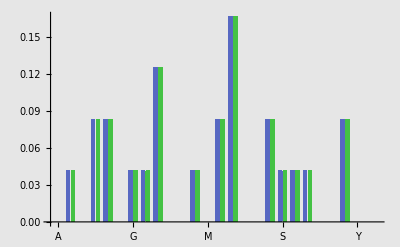

```mathematica
BEZGraphRelFreq[PT,CT]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Transposition cipher cryptanalysis

We can analyze the transposition cipher using bigram analysis. We search the ciphertext for frequent bigrams that are split by a fixed amount of characters. For English, the most frequent bigrams are: TH, HE, AN, RE, ER, IN, ON, AT, ND, ST, ES, EN, OF, TE. From the distance of characters in we can determine the parameter of transposition that was used. For example, let us have the following ciphertext: TDIRHIEOESDNGBIOOUNXLROX. We immediately see the bigrams TH a HE split to a distance of 4, which means that the matrix had 4 rows:

```mathematica
BEZTranspose["TDIRHIEOESDNGBIOOUNXLROX",4]
```

THEGOLDISBURIEDINORONOXX

Another possibility is to factor the length of text and thus get all divisors of the length and try them one at a time.

```mathematica
FactorInteger[StringLength["TDIRHIEOESDNGBIOOUNXLROX"]]/.{x_Integer,y_Integer}->HoldForm[x^y]
```

{2^3,3^1}

In this case we see that the length of text is 24 characters, which may have been created as 2*12, 3*8, 4*6, 6*4, 8*3, or 12*2. Other combinations do not exist. In our case, the transposition matrix was 6*4.

If the text was not exactly as long as required to fill the matrix, padding was added. In our simple cipher, we see that the character X is always used as padding. This fact can be used to break the transposition cipher, because the distance in this padding (in case of more than one X) gives the out transposition constant immediately. Length of text divided by the transposition constant gives the reverse transposition constant.

In our case, the distance in padding is 4 chahracters.

Note: If we use the transposition multiple times (or permute the coumns etc.), the cryptanalysis can be substantially more difficult!

```mathematica
BEZTranspose[BEZTranspose["THEGOLDISBURIEDINORONO",4],3]
```

TIHEEDGIONLODRIOSNBOUXRX

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Task 3: Transposition cipher cryptanalysis

Write/copy a fragment of English text about 30-50 characters long and choose a random transposition constant. Encrypt this text by transposition and send the ciphertext to your neighbor.

```mathematica
PT="ITSNOTATIMEFORWARITSATIMEFORPEACE"
```

ITSNOTATIMEFORWARITSATIMEFORPEACE

```mathematica
BEZTranspose[PT,11]
```

IFITOMSRENWFOAOTRRAIPTTEISAMACETE

After you get a cryptogram of your neighbor, assign it into this variable:

```mathematica
CT="IUPNUWLOAFRPDKIAUNYHYYNTPRDOAAOOCYHS"
```

IUPNUWLOAFRPDKIAUNYHYYNTPRDOAAOOCYHS

Now try to break the cipher. Use some of the method described above. An example of factoring the ciphertext length is repeated here.

```mathematica
FactorInteger[StringLength[CT]]/.{x_Integer,y_Integer}->HoldForm[x^y]
```

```mathematica
BEZTranspose[CT,9]
```

IFYOURHAPPYANDYOUKNOWITCLAPYOURHANDS